```mathematica
files = FileNames["*.tab"];
datas = Drop[Import[#], 1]&/@files;
ch1s=Transpose[{#[[All,1]],#[[All,2]]}]&/@datas;
ch2s=Transpose[{#[[All,1]],#[[All,3]]}]&/@datas;
data = Transpose[{ch1s, ch2s}];
filterdata = data[[ ;; 13]];
foehndata = data[[14 ;; ]];
fitdata =Select[filterdata[[8, 1]], #[[1]]≥ 0 && #[[1]]≤0.012&];
```

```mathematica
fitdata = Table[Select[data[[i, 2]], #[[1]]≥ 0.0054 && #[[1]]≤0.013&], {i, 1, Length[data]}];
nlms = NonlinearModelFit[#, a - b ⅇ^(-c x), {a, b, c}, x]&/@fitdata;
funcs = Normal[#]&/@ nlms;
```

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

NonlinearModelFit::nrlnum: The function value {0.00538545  - 1.\ "", 0.00539042  - 1.\ "", 0.00539539  - 1.\ "", 0.00540037  - 1.\ "", 0.00540534  - 1.\ "", 0.00541031  - 1.\ "", 0.00541528  - 1.\ "", 0.00542026  - 1.\ "", 0.00542523  - 1.\ "", « 34 », 0.00559927  - 1.\ "", 0.00560424  - 1.\ "", 0.00560921  - 1.\ "", 0.00561418  - 1.\ "", 0.00561915  - 1.\ "", 0.00562413  - 1.\ "", 0.0056291  - 1.\ "", « 916 »} is not a list of real numbers with dimensions {966} at {a, b, c} = {1., 1., 1.}.

NonlinearModelFit::nrlnum: The function value {0.00538545  - 1.\ "", 0.00539539  - 1.\ "", 0.00540534  - 1.\ "", 0.00541528  - 1.\ "", 0.00542523  - 1.\ "", 0.00543518  - 1.\ "", 0.00544512  - 1.\ "", 0.00545507  - 1.\ "", 0.00546501  - 1.\ "", « 34 », 0.00581304  - 1.\ "", 0.00582298  - 1.\ "", 0.00583292  - 1.\ "", 0.00584286  - 1.\ "", 0.00585281  - 1.\ "", 0.00586275  - 1.\ "", 0.00587269  - 1.\ "", « 711 »} is not a list of real numbers with dimensions {761} at {a, b, c} = {1., 1., 1.}.

General::stop: Further output of NonlinearModelFit :: nrlnum will be suppressed during this calculation.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit :: fitd will be suppressed during this calculation.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

NonlinearModelFit::nrlnum: The function value {0.00538545  - 1.\ "", 0.00539042  - 1.\ "", 0.00539539  - 1.\ "", 0.00540037  - 1.\ "", 0.00540534  - 1.\ "", 0.00541031  - 1.\ "", 0.00541528  - 1.\ "", 0.00542026  - 1.\ "", 0.00542523  - 1.\ "", « 34 », 0.00559927  - 1.\ "", 0.00560424  - 1.\ "", 0.00560921  - 1.\ "", 0.00561418  - 1.\ "", 0.00561915  - 1.\ "", 0.00562413  - 1.\ "", 0.0056291  - 1.\ "", « 916 »} is not a list of real numbers with dimensions {966} at {a, b, c} = {1., 1., 1.}.

NonlinearModelFit::nrlnum: The function value {0.00538545  - 1.\ "", 0.00539539  - 1.\ "", 0.00540534  - 1.\ "", 0.00541528  - 1.\ "", 0.00542523  - 1.\ "", 0.00543518  - 1.\ "", 0.00544512  - 1.\ "", 0.00545507  - 1.\ "", 0.00546501  - 1.\ "", « 34 », 0.00581304  - 1.\ "", 0.00582298  - 1.\ "", 0.00583292  - 1.\ "", 0.00584286  - 1.\ "", 0.00585281  - 1.\ "", 0.00586275  - 1.\ "", 0.00587269  - 1.\ "", « 711 »} is not a list of real numbers with dimensions {761} at {a, b, c} = {1., 1., 1.}.

General::stop: Further output of NonlinearModelFit :: nrlnum will be suppressed during this calculation.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit :: fitd will be suppressed during this calculation.

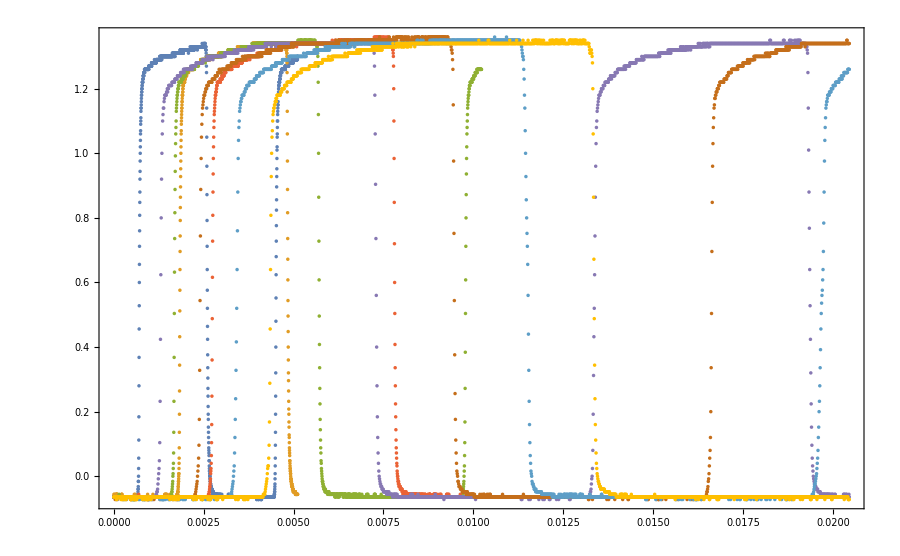

```mathematica
ListPlot[filterdata[[#,1]]&/@Range[8],ImageSize->900,Frame->True]
```

```mathematica
nlm= NonlinearModelFit[fitdata,{ a/(1+Exp[(-x+μ)/(σ*10^-3)])+b-Piecewise[{{0,x<μ},{ c Exp[-d x],x≥μ}}],a<10,b<0,b>-0.1,c>0,c<5,d>0,d<1000,σ>0,σ<0.1,μ<0.005,μ>0.004}, {{a,2},{b,-0.07},{μ,0.0043},{σ,0.03},{c,2},{d,500}}, x]
nlm["ParameterTable"]
```

FittedModel[-0.0640119+1.40824/(1+ⅇ^(60073.5 («21»-x)))-(Piecewise[{{0, x<0.00435495}, {4.99996 ⅇ^(-756.007 x), x≥0.00435495}, {0, True}}])]

FittedModel::constr: The property values {"ParameterTable"} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
a | 1.40824 | 0.000611843 | 2301.64 | 2.49734066031×10^-2181
b | -0.0640119 | 0.000371353 | -172.375 | 1.91257508489×10^-846
μ | 0.00435495 | 1.81289×10^-7 | 24022.1 | 1.81509656605×10^-3398
σ | 0.0166463 | 0.000162069 | 102.711 | 2.4366841344×10^-595
c | 4.99996 | 0.270885 | 18.4579 | 3.97406×10^-67
d | 756.007 | 11.3417 | 66.6571 | 6.87713535923×10^-405

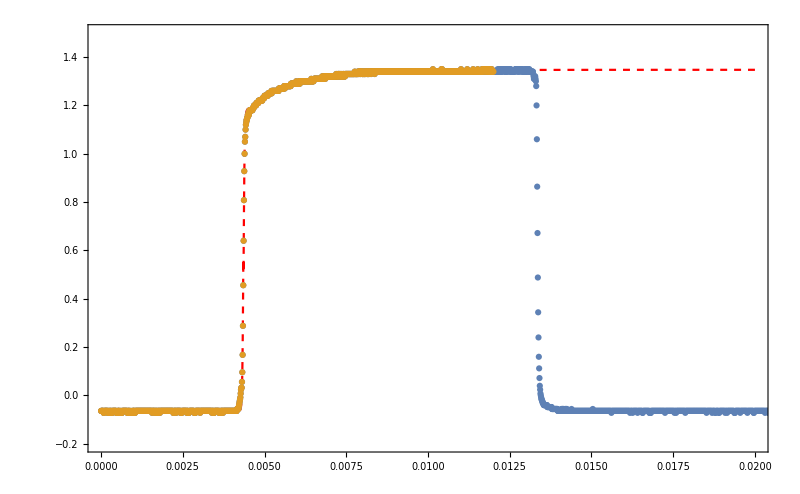

```mathematica
Show[Plot[Normal[nlm],{x,0,0.02},ImageSize->800,Frame->True,PlotRange->{-0.2,1.5},ImageSize->500,Frame->True, PlotStyle->{Red, Dashed}],ListPlot[{filterdata[[8,1]],fitdata}]]
```

```mathematica
Manipulate[Show[Plot[{Normal[nlm], c/(1+Exp[(-x+0.0043)/0.00003])-0.06-Piecewise[{{0,x<0.0043},{a Exp[-b x],x≥0.0043}}]},{x,0,0.02},ImageSize->800,Frame->True,PlotRange->{-0.2,3},ImageSize->500,Frame->True, PlotStyle->{Red, Dashed}],ListPlot[{filterdata[[8,1]],fitdata}]],{a,1,10},{b,0,1000},{c,1,5}]
```

Part::partd: Part specification filterdata ⟦ 8, 1 ⟧ is longer than depth of object.

General::ivar: 4.08571×10^-7 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

```mathematica
nlms = NonlinearModelFit[#, a - b ⅇ^(-c x), {a, b, c}, x]&/@fitdata;
```

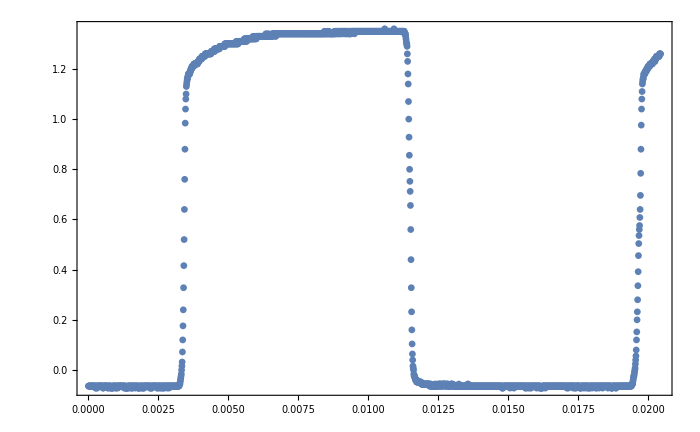

```mathematica
ListPlot[filterdata[[7,1]],ImageSize->700,Frame->True]
```

```mathematica
einsatz={{{0.0007778,1.186}},{{0.001905,1.179}},{{0.001759,1.175}},{{0.002808,1.169}},{{0.001421,1.16}},{{0.002485,1.158}},{{0.003456,1.143}},{{0.004395,1.13}},{{0.005459,1.119}},{{0.006711,1.112}},{{0.005196,1.115}},{{0.01114,1.097}},{{0.03011,1.161}}};
fallend={{{0.002593,0.6409}},{{0.004839,0.6786}},{{0.005703,0.6157}},{{0.007769,0.7189}},{{0.007306,0.7321}},{{0.009466,0.7529}},{{0.01147,0.7529}},{{0.01338,0.672}},{{0.01541,0.6945}},{{0.01786,0.6394}},{{0.02186,0.6795}},{{0.03376,0.6269}},{{0.08176,0.647}}};
```

{1.186,1.179,1.175,1.169,1.16,1.158,1.143,1.13,1.119,1.112,1.115,1.097,1.161}

{1.8152,2.934,3.944,4.961,5.885,6.981,8.014,8.985,9.951,11.149,16.664,22.62,51.65}

{{1.8152,1.186},{2.934,1.179},{3.944,1.175},{4.961,1.169},{5.885,1.16},{6.981,1.158},{8.014,1.143},{8.985,1.13},{9.951,1.119},{11.149,1.112},{16.664,1.115},{22.62,1.097},{51.65,1.161}}

{{1.8152,1.186},{2.934,1.179},{3.944,1.175},{4.961,1.169},{5.885,1.16},{6.981,1.158},{8.014,1.143},{8.985,1.13},{9.951,1.119},{11.149,1.112}}

FittedModel[1.09335+0.12 ⅇ^(-0.116905 x)]

FittedModel::constr: The property values {"ParameterTable"} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
a | 8.55393 | 8.7754 | 0.974762 | 0.362152
min | 1.09335 | 0.0606636 | 18.0231 | 4.00084×10^-7
amp | 0.12 | 0.0453137 | 2.6482 | 0.0330277

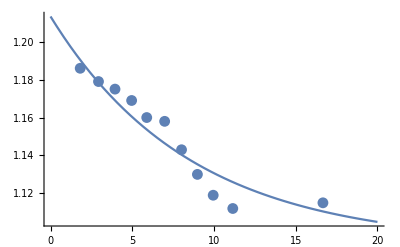

```mathematica
einsatz2=einsatz[[All,1,2]]
T=(fallend[[All,1,1]]-einsatz[[All,1,1]])*10^3
plotdata=Transpose[{T,einsatz2}]
fitdata=Drop[plotdata,-3]
nlm=NonlinearModelFit[fitdata,{min+amp Exp[-x/a],amp>0,amp<0.12},{a,min,amp},x]
nlm["ParameterTable"]
Show[Plot[Normal[nlm],{x,0,20}],ListPlot[plotdata,PlotRange->{1,1.3}]]
```